## Appendix to manuscript entitled “Modifier Theory: The Population Genetics of Biological Noise” by DM Weinreich et al.

#### 25 October 2025: Initial Version

If phenotype z_realized ~ N(z_0, σ^2) (Eqn 1 in ms) and Malthusian fitness r(z_realized) = r_optimum - z_realized^2 (Eqn 2 in ms), we seek the probability density function for z_realized using the change-of-value technique shown at https://online.stat.psu.edu/stat414/lesson/22/22.3.

Because selection acts on differences in Malthusian fitness, results are independent of r_optimum. So without loss of generality I set that to zero.

As shown below, this is 

	fR[r,z0,σ] = (ⅇ^(-(-√-r-z0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])+(ⅇ^(-(√-r-z0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])					Eqn A1

Using A1, we can now find the expected fitness effect of noise as a function of z_0 and σ, as well as it expectation conditioned on realizing a beneficial phenotype, i.e., on z_realized > z_0. Also as shown below, these are

	Er[z0,σ] ≡ ∫_(-∞)^0 fR[[r,z0,σ]rⅆr = -(z0^2+σ^2)									Eqn A2

and

	ErBeneficial[z0,σ]  ≡ (∫_(-z0^2)^0 fR[r,z0,σ]rⅆr)/(∫_(-z0^2)^0 fR[r,z0,σ]ⅆr) = 					Eqn A3
		{2 Abs[z0] √(2/π) σ+(z0^2+σ^2) 
(Erf[(z0-√(z0^2))/(√2 σ)]-Erf[(z0+√(z0^2))/(√2 σ)])}/Erf[(Abs[z0] √2)/σ]		

Eqns A1 - A3  exactly match simulation results developed in MatLab (not shown).

Elements of Figure 2 are also developed here.

Notation: fZ[] is the PDF of z_realized (Eq 1 in the ms), and v1[] and v2[] are the piece-wise inversions of the the function r(z_realized) = -r_realized^2 (Eq 2). fR[] is the PDF we seek.

```mathematica
fZ[z_,z0_,σ_] :=PDF[NormalDistribution[z0,σ],z];
v1[y_]:=-Sqrt[-y];
v2[y_]:=Sqrt[-y];
```

The recipe from the website is fR(r) = fZ(v1(r)) • |v1’(r)| + fZ(v2(r)) • |v2’(r)|

```mathematica
fR[r_,z0_,σ_]:=fZ[v1[r],z0,σ]*Abs[v1'[r]]+fZ[v2[r],z0,σ]*Abs[v2'[r]];
```

Say it out loud so that I can code it up in my MatLab simulations.

```mathematica
Clear[z0,σ]
fR[r,z0,σ]
```

(ⅇ^(-(-√-r-z0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])+(ⅇ^(-(√-r-z0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])

Is it a PDF? Yes! (Though I do wonder why Mathematic won’t simplify this answer as 1. Even if there were an imaginary part to σ, I don’t see why the two pieces wouldn’t cancel out...)

```mathematica
Clear[z0,σ];
∫_-Infinity^0 fR[r,z0,σ]ⅆr
```

ConditionalExpression[√(1/σ^2) σ, Re[σ^2]≥0]

What is the expected fitness over all noise?

```mathematica
Clear[z0,σ];
FullSimplify[∫_-Infinity^0 (fR[r,z0,σ]*r)ⅆr]
```

ConditionalExpression[-√(1/σ^2) σ (z0^2+σ^2), Re[σ^2]≥0]

As with the proof that fR[] is a pdf above, Mathematica doesn’t want to simplify (√(1/σ^2) σ) as 1.  But I’m going to write that as 1 here.

```mathematica
Er[z0_,σ_]:=- (z0^2+σ^2);
```

And finally, the expected fitness over beneficial noise? First the numerator.

```mathematica
Clear[z0,σ];
FullSimplify[∫_(-(z0^2))^0 (fR[r,z0,σ]*r)ⅆr]
```

1/2 √(z0/Conjugate[z0]) (2 √(2/π) √(z0^2) σ+(z0^2+σ^2) (Erf[(z0-√(z0^2))/(√2 σ)]-Erf[(z0+√(z0^2))/(√2 σ)]))

And now the denominator, needed to make our result a PDF.

```mathematica
Clear[z0,σ];
FullSimplify[∫_(-(z0^2))^0 fR[r,z0,σ]ⅆr]
```

∫_(-z0^2)^0 (ⅇ^((r-z0 (2 √-r+z0))/(2 σ^2)) (1+ⅇ^((2 √-r z0)/σ^2)))/(2 √(2 π) σ √Abs[r])ⅆr

Seems that Mathematica can’t get there for arbitrary z0, so here’s what it looks like for a few specific values

```mathematica
z0:=1;
FullSimplify[∫_(-(z0^2))^0 fR[r,z0,σ]ⅆr]
z0:=-2;
FullSimplify[∫_(-(z0^2))^0 fR[r,z0,σ]ⅆr]
z0:=3;
FullSimplify[∫_(-(z0^2))^0 fR[r,z0,σ]ⅆr]
```

1/2 Erf[(√2)/σ]

1/2 Erf[(2 √2)/σ]

1/2 Erf[(3 √2)/σ]

Looking at the above suggests that the answer is 1/2 Erf[(Abs[z0] √2)/s]. That gives

```mathematica
ErBeneficial[z0_,σ_]:=(2 Abs[z0] √(2/π) σ+(z0^2+σ^2) (Erf[(z0-√(z0^2))/(√2 σ)]-Erf[(z0+√(z0^2))/(√2 σ)]))/Erf[(Abs[z0] √2)/σ];
```

#### Figures

Here’s the y-axis of Figure 2A. The second panel illustrates that the peak at r_optimum in the first is extremely narrow, so I truncated it from the ms to reduce confusion for the reader.

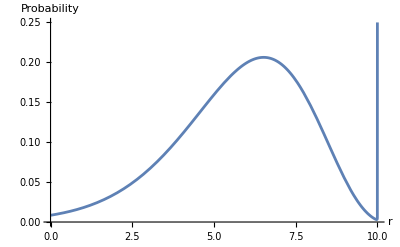

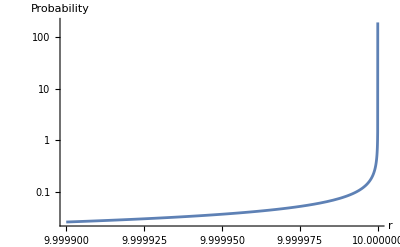

```mathematica
ropt:=10;
z0:=-2;
σLowNoise:=0.5;
Plot[fR[r-ropt,z0,σLowNoise],{r,0,10},PlotRange->{0,0.25},AxesLabel->{"r","Probability"}]
LogPlot[fR[r-ropt,z0,σLowNoise],{r,9.9999,10},PlotRange->All,AxesLabel->{"r","Probability"}]
```

Here’s the y-axis for Figure 2B

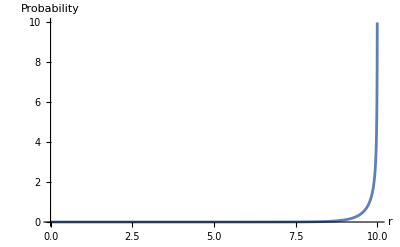

```mathematica
z0:=0;
Plot[fR[r-ropt,z0,σLowNoise],{r,0,10},AxesLabel->{"r","Probability"},PlotRange->{0,10}]
```

Here’s Figure 2C

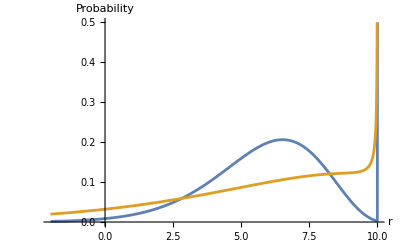

```mathematica
z0:=-2;
σHighNoise:=1;
Plot[{fR[r-ropt,z0,σLowNoise],fR[r-ropt,z0,σHighNoise]},{r,-2,10},PlotRange->{0,.5},AxesLabel->{"r","Probability"}]
```

Here’s Fig 2D

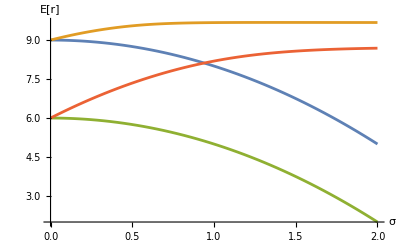

```mathematica
Plot[{ropt+Er[1,σ],ropt+ErBeneficial[1,σ],ropt+Er[2,σ],ropt+ErBeneficial[2,σ]},{σ,0,2},AxesLabel->{"σ","E[r]"}]
```